```mathematica
Clear[phystest];
Clear[zero];
Clear[Σ];
Clear[Subscript[a, 1]];
Clear[Subscript[a, 2]];
Clear[Subscript[a, 3]];
Clear[SuperPlus[Subscript[e, 12]]];
Clear[SuperMinus[Subscript[e, 12]]];
Clear[SuperPlus[Subscript[e, 23]]];
Clear[SuperMinus[Subscript[e, 23]]];
Clear[SuperPlus[Subscript[e, 13]]];
Clear[SuperMinus[Subscript[e, 13]]];
Clear[b1];
Clear[b2];
Clear[b3];
Clear[c1];
Clear[c2];
Clear[c3];
Clear[cp];
Clear[cm];
Clear[covm];
```

Clear::ssym: a_1 is not a symbol or a string.

Clear::ssym: a_2 is not a symbol or a string.

Clear::ssym: a_3 is not a symbol or a string.

Clear::ssym: (e_12)^+ is not a symbol or a string.

Clear::ssym: (e_12)^- is not a symbol or a string.

Clear::ssym: (e_23)^+ is not a symbol or a string.

Clear::ssym: (e_23)^- is not a symbol or a string.

Clear::ssym: (e_13)^+ is not a symbol or a string.

Clear::ssym: (e_13)^- is not a symbol or a string.

```mathematica
c1=Table[RandomReal[{1,100}],{i,10^2}];
c2=Table[RandomReal[{1,100}],{i,10^2}];
c3=Table[RandomReal[{1,100}],{i,10^2}];
```

```mathematica
a1=Table[c1[[i]]-1,{i,1,Length[c1]}];
a2=Table[c2[[i]]-1,{i,1,Length[c2]}];
a3=Table[c3[[i]]-1,{i,1,Length[c3]}];

(*these values a1,a2,a3 are all greater than 0*)

c1[[1]]
a1[[1]]
```

86.0077

85.0077

```mathematica
a1
```

{85.0077,8.13477,6.45699,87.686,51.2206,76.0735,60.1392,51.333,7.1977,52.3376,44.2566,13.1248,36.1024,85.9186,96.4612,75.2047,59.4873,64.5211,40.1013,41.7754,54.8211,97.2552,81.2458,77.2094,13.5336,97.7235,87.9905,33.1011,10.2636,87.2802,14.5607,70.1079,39.4672,93.0576,23.4956,34.5835,10.7331,90.7391,2.09851,29.3536,47.2572,92.0889,30.6682,22.0792,58.4748,86.216,42.2339,73.5598,65.2123,85.5591,50.7996,70.2276,56.6734,59.3398,68.1638,37.0771,61.5166,72.0431,98.8117,58.7963,98.7404,86.2866,71.7825,16.4736,88.2181,28.0967,55.3107,12.6159,10.8192,85.8625,33.3339,35.9147,71.6666,19.74,98.2064,91.8654,20.8416,72.2097,57.3792,47.9684,53.1717,73.6355,43.8523,1.63038,46.604,1.8378,59.7387,91.66,61.0893,56.0011,42.6376,17.702,2.70251,57.8568,78.232,62.8588,26.4052,98.3186,65.3703,50.7103}

```mathematica
a2;
```

```mathematica
a3;
```

```mathematica
b1={};
b2={};
b3={};
```

```mathematica
Do[If[Abs[a1[[i]]-a2[[i]]]<a3[[i]]<a1[[i]]+a2[[i]]&&Abs[a1[[i]]-a3[[i]]]<a2[[i]]<a1[[i]]+a3[[i]]
&&Abs[a2[[i]]-a3[[i]]]<a1[[i]]<a2[[i]]+a3[[i]]
,Print[{i ,a1[[i]],a2[[i]],a3[[i]]}],Print["NO"]]
,{i,1,Length[a1]}];

(*Only currently evaluating the first inequality, need to refine the values of aj[[i]] more to include the second 2 inequalities also.*)
```

NO

NO

NO

{4,87.686,74.1144,80.6976}

NO

{6,76.0735,68.7478,72.2557}

{7,60.1392,72.7579,12.6294}

NO

NO

{10,52.3376,77.4925,49.8254}

NO

NO

{13,36.1024,57.0189,27.7676}

{14,85.9186,31.4393,81.5033}

{15,96.4612,79.8977,35.3618}

NO

NO

{18,64.5211,21.4566,74.067}

{19,40.1013,88.4382,84.6265}

{20,41.7754,71.9387,87.8483}

NO

NO

{23,81.2458,76.8129,9.72625}

{24,77.2094,54.1932,51.5435}

NO

{26,97.7235,38.135,89.1913}

{27,87.9905,28.228,63.8185}

{28,33.1011,45.7055,74.9119}

{29,10.2636,19.5563,10.3457}

NO

NO

{32,70.1079,59.803,77.2427}

NO

{34,93.0576,87.3669,27.6284}

NO

NO

NO

«5 more identical outputs»

{43,30.6682,75.1965,97.8871}

NO

NO

{46,86.216,18.5038,69.2705}

NO

{48,73.5598,79.2287,51.3986}

{49,65.2123,90.7499,38.8969}

NO

NO

NO

«1 more identical outputs»

{54,59.3398,56.4022,86.7294}

{55,68.1638,73.2584,23.2223}

{56,37.0771,78.0745,71.4558}

{57,61.5166,27.8421,47.3495}

{58,72.0431,49.0397,98.4217}

{59,98.8117,71.6224,41.3033}

NO

NO

NO

{63,71.7825,67.7027,78.9509}

NO

NO

{66,28.0967,60.0679,44.535}

{67,55.3107,9.09157,46.555}

{68,12.6159,77.6508,71.785}

NO

NO

{71,33.3339,71.1855,63.9498}

{72,35.9147,47.824,12.8399}

{73,71.6666,68.1749,60.0111}

{74,19.74,22.5044,10.2921}

{75,98.2064,34.5937,77.7409}

NO

NO

{78,72.2097,73.7921,60.0477}

NO

{80,47.9684,48.2758,82.097}

NO

{82,73.6355,16.2807,57.7207}

NO

NO

NO

«1 more identical outputs»

{87,59.7387,95.069,96.5171}

{88,91.66,90.4316,73.7638}

NO

{90,56.0011,51.3594,74.7887}

{91,42.6376,42.5066,1.09798}

{92,17.702,3.33013,15.9948}

NO

NO

{95,78.232,82.6377,17.9367}

{96,62.8588,80.6119,92.2248}

{97,26.4052,24.7515,32.7202}

NO

{99,65.3703,71.8884,89.7137}

{100,50.7103,53.9204,38.3537}

```mathematica
Do[If[Abs[a1[[i]]-a2[[i]]]<a3[[i]]<a1[[i]]+a2[[i]]&&Abs[a1[[i]]-a3[[i]]]<a2[[i]]<a1[[i]]+a3[[i]]
&&Abs[a2[[i]]-a3[[i]]]<a1[[i]]<a2[[i]]+a3[[i]]
,AppendTo[b1,a1[[i]]]&&AppendTo[b2,a2[[i]]]&&AppendTo[b3,a3[[i]]];]
,{i,1,Length[a1]}];
```

```mathematica
b1
```

{87.686,76.0735,60.1392,52.3376,36.1024,85.9186,96.4612,64.5211,40.1013,41.7754,81.2458,77.2094,97.7235,87.9905,33.1011,10.2636,70.1079,93.0576,30.6682,86.216,73.5598,65.2123,59.3398,68.1638,37.0771,61.5166,72.0431,98.8117,71.7825,28.0967,55.3107,12.6159,33.3339,35.9147,71.6666,19.74,98.2064,72.2097,47.9684,73.6355,59.7387,91.66,56.0011,42.6376,17.702,78.232,62.8588,26.4052,65.3703,50.7103}

```mathematica
b2;
```

```mathematica
b3;
```

```mathematica
Subscript[a, 1]=Table[b1[[i]]+1,{i,1,Length[b1]}];
Subscript[a, 2]=Table[b2[[i]]+1,{i,1,Length[b2]}];
Subscript[a, 3]=Table[b3[[i]]+1,{i,1,Length[b3]}];
```

```mathematica
Subscript[a, 1]
```

{88.686,77.0735,61.1392,53.3376,37.1024,86.9186,97.4612,65.5211,41.1013,42.7754,82.2458,78.2094,98.7235,88.9905,34.1011,11.2636,71.1079,94.0576,31.6682,87.216,74.5598,66.2123,60.3398,69.1638,38.0771,62.5166,73.0431,99.8117,72.7825,29.0967,56.3107,13.6159,34.3339,36.9147,72.6666,20.74,99.2064,73.2097,48.9684,74.6355,60.7387,92.66,57.0011,43.6376,18.702,79.232,63.8588,27.4052,66.3703,51.7103}

```mathematica
SuperPlus[Subscript[e, 12]]=Table[
(√(((Subscript[a, 1][[i]]-Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]-1)^2)((Subscript[a, 1][[i]]-Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]+1)^2))+√(((Subscript[a, 1][[i]]+Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]-1)^2)((Subscript[a, 1][[i]]+Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]+1)^2)))/(4 √(Subscript[a, 1][[i]]Subscript[a, 2][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
SuperMinus[Subscript[e, 12]]=Table[
(√(((Subscript[a, 1][[i]]-Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]-1)^2)((Subscript[a, 1][[i]]-Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]+1)^2))-√(((Subscript[a, 1][[i]]+Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]-1)^2)((Subscript[a, 1][[i]]+Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]+1)^2)))/(4 √(Subscript[a, 1][[i]]Subscript[a, 2][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
SuperPlus[Subscript[e, 23]]=Table[
(√(((Subscript[a, 2][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]-1)^2)((Subscript[a, 2][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]+1)^2))+√(((Subscript[a, 2][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]-1)^2)((Subscript[a, 2][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]+1)^2)))/(4 √(Subscript[a, 2][[i]]Subscript[a, 3][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
SuperMinus[Subscript[e, 23]]=Table[
(√(((Subscript[a, 2][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]-1)^2)((Subscript[a, 2][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]+1)^2))-√(((Subscript[a, 2][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]-1)^2)((Subscript[a, 2][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]+1)^2)))/(4 √(Subscript[a, 2][[i]]Subscript[a, 3][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
SuperPlus[Subscript[e, 13]]=Table[
(√(((Subscript[a, 1][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]-1)^2)((Subscript[a, 1][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]+1)^2))+√(((Subscript[a, 1][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]-1)^2)((Subscript[a, 1][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]+1)^2)))/(4 √(Subscript[a, 1][[i]]Subscript[a, 3][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
SuperMinus[Subscript[e, 13]]=Table[
(√(((Subscript[a, 1][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]-1)^2)((Subscript[a, 1][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]+1)^2))-√(((Subscript[a, 1][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]-1)^2)((Subscript[a, 1][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]+1)^2)))/(4 √(Subscript[a, 1][[i]]Subscript[a, 3][[i]])),{i,1,Length[Subscript[a, 1]]}]//FullSimplify;
```

```mathematica
Subscript[σ, SF]=Table[{{Subscript[a, 1][[i]],0,SuperPlus[Subscript[e, 12]][[i]],0, SuperPlus[Subscript[e, 13]][[i]],0},{0,Subscript[a, 1][[i]],0,SuperMinus[Subscript[e, 12]][[i]],0,SuperMinus[Subscript[e, 13]][[i]]},{SuperPlus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0, SuperPlus[Subscript[e, 23]][[i]],0},{0,SuperMinus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0,SuperMinus[Subscript[e, 23]][[i]]},{SuperPlus[Subscript[e, 13]][[i]],0,SuperPlus[Subscript[e, 23]][[i]],0, Subscript[a, 3][[i]],0},{0,SuperMinus[Subscript[e, 13]][[i]],0,SuperMinus[Subscript[e, 23]][[i]],0,Subscript[a, 3][[i]]}},{i,1,Length[Subscript[a, 1]]}];
```

```mathematica
Subscript[σ, SF][[1]]
```

{{88.686,0,81.6103,0,85.1128,0},{0,88.686,0,-41.8567,0,-52.2632},{81.6103,0,75.1144,0,78.3275,0},{0,-41.8567,0,75.1144,0,-28.4094},{85.1128,0,78.3275,0,81.6976,0},{0,-52.2632,0,-28.4094,0,81.6976}}

```mathematica
Eigenvalues[Subscript[σ, SF][[1]]]
```

{245.481,140.485,105.009,0.00952301,0.00711819,0.00407363}

```mathematica
(*All eigenvalues now real and positive therefore we have physical states*)
```

```mathematica
Subscript[σ, PT1]=Table[{{Subscript[a, 1][[i]],0,SuperPlus[Subscript[e, 12]][[i]],0, SuperPlus[Subscript[e, 13]][[i]],0},{0,Subscript[a, 1][[i]],0,-SuperMinus[Subscript[e, 12]][[i]],0,-SuperMinus[Subscript[e, 13]][[i]]},{SuperPlus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0, SuperPlus[Subscript[e, 23]][[i]],0},{0,-SuperMinus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0,SuperMinus[Subscript[e, 23]][[i]]},{SuperPlus[Subscript[e, 13]][[i]],0,SuperPlus[Subscript[e, 23]][[i]],0, Subscript[a, 3][[i]],0},{0,-SuperMinus[Subscript[e, 13]][[i]],0,SuperMinus[Subscript[e, 23]][[i]],0,Subscript[a, 3][[i]]}},{i,1,Length[Subscript[a, 1]]}];
```

```mathematica
Subscript[σ, PT2]=Table[{{Subscript[a, 1][[i]],0,SuperPlus[Subscript[e, 12]][[i]],0, SuperPlus[Subscript[e, 13]][[i]],0},{0,Subscript[a, 1][[i]],0,-SuperMinus[Subscript[e, 12]][[i]],0,SuperMinus[Subscript[e, 13]][[i]]},{SuperPlus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0, SuperPlus[Subscript[e, 23]][[i]],0},{0,-SuperMinus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0,-SuperMinus[Subscript[e, 23]][[i]]},{SuperPlus[Subscript[e, 13]][[i]],0,SuperPlus[Subscript[e, 23]][[i]],0, Subscript[a, 3][[i]],0},{0,SuperMinus[Subscript[e, 13]][[i]],0,-SuperMinus[Subscript[e, 23]][[i]],0,Subscript[a, 3][[i]]}},{i,1,Length[Subscript[a, 1]]}];
```

```mathematica
Subscript[σ, PT3]=Table[{{Subscript[a, 1][[i]],0,SuperPlus[Subscript[e, 12]][[i]],0, SuperPlus[Subscript[e, 13]][[i]],0},{0,Subscript[a, 1][[i]],0,SuperMinus[Subscript[e, 12]][[i]],0,-SuperMinus[Subscript[e, 13]][[i]]},{SuperPlus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0, SuperPlus[Subscript[e, 23]][[i]],0},{0,SuperMinus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0,-SuperMinus[Subscript[e, 23]][[i]]},{SuperPlus[Subscript[e, 13]][[i]],0,SuperPlus[Subscript[e, 23]][[i]],0, Subscript[a, 3][[i]],0},{0,-SuperMinus[Subscript[e, 13]][[i]],0,-SuperMinus[Subscript[e, 23]][[i]],0,Subscript[a, 3][[i]]}},{i,1,Length[Subscript[a, 1]]}];
```

{{9.05891,0,-1.80664,0},{0,9.05891,0,-3.84297},{-1.80664,0,5.39379,0},{0,-3.84297,0,5.39379}}

```mathematica
Clear[phystest]
```

```mathematica
phystest={};
Do[AppendTo[phystest,{Eigenvalues[Subscript[σ, SF][[i]]]}];,{i,1,Length[Subscript[σ, SF]]}]
```

```mathematica
phystest;
```

```mathematica
Length[phystest]
```

50

```mathematica
Table[{i,Min[phystest[[i]]]},{i,1,Length[Subscript[σ, SF]]}];
```

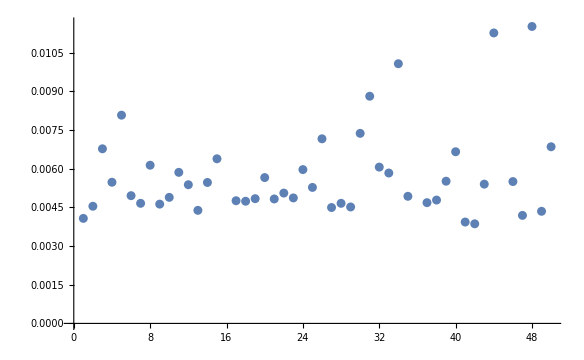

```mathematica
ListPlot[Table[{i,Min[phystest[[i]]]},{i,1,Length[Subscript[σ, SF]]}]]
```

```mathematica
Dynamic[i]
```

```mathematica
covmpt=Table[{{a[[i]],0,cp[[i]],0},{0,a[[i]],0,-cm[[i]]},{cp[[i]],0,b[[i]],0},{0,-cm[[i]],0,b[[i]]}},{i,10^5}];
```

```mathematica
(*partially transposed cov matrix)
```

```mathematica
phystest2={};
Do[AppendTo[phystest2,{Abs[Eigenvalues[ⅈ Σ . covmpt[[i]]//Chop]]}];,{i,1,Length[covmpt]}]


phystest2[[200]]
```

{{144.562,144.562,0.948294,0.948294}}

```mathematica
Table[{i,{Min[phystest2[[i]]]}},{i,1,Length[cm]}];
Min[phystest2[[1]]]
```

0.258571

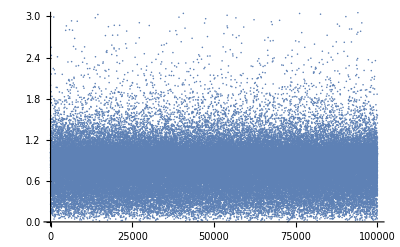

```mathematica
ListPlot[Table[{i,Min[phystest2[[i]]]},{i,10^5}],PlotRange->{0,3}]
(*Points that are less than 1 are entangled and greater than one are seperable*)
```

```mathematica
SympEig={};
Do[AppendTo[SympEig,Min[Abs[Eigenvalues[ⅈ Σ . covmpt[[i]]]]//Chop]];,{i,10^5}];
```

```mathematica
Dynamic[i]
```

```mathematica
SympEig[[1]]
```

0.504792

```mathematica
Table[{i,{SympEig[[i]]}},{i,10^5}];
```

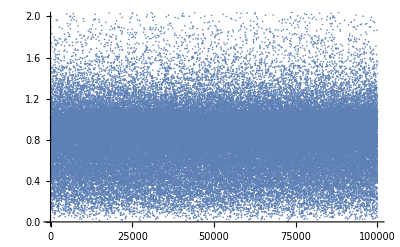

```mathematica
ListPlot[Table[{i,SympEig[[i]]},{i,10^5}],PlotRange->{0,2}]
```

```mathematica
Negativity={};
Do[AppendTo[Negativity,(1-SympEig[[i]])/(2SympEig[[i]])];,{i,10^5}];
Negativity[[1]]
```

1.4337

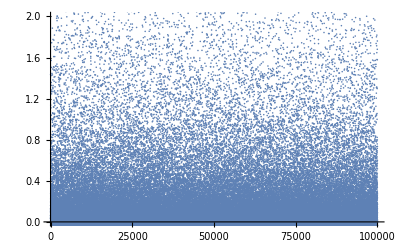

```mathematica
Table[{i,{Negativity[[i]]}},{i,10^5}];
ListPlot[Table[{i,Negativity[[i]]},{i,10^5}],PlotRange->{0,2}]
```

```mathematica
LogNeg={};
Do[AppendTo[LogNeg,-Log[SympEig[[i]]]];,{i,10^5}];
LogNeg[[1]]
```

1.35258

```mathematica
Dynamic[i]
```

```mathematica
Table[{i,{LogNeg[[i]]}},{i,10^5}];
```

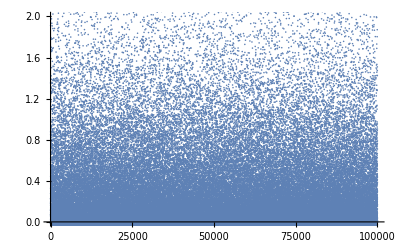

```mathematica
ListPlot[Table[{i,LogNeg[[i]]},{i,10^5}],PlotRange->{0,2}]
```

```mathematica
Subscript[Determinantσ, P.T]={};
```

```mathematica
Do[AppendTo[Subscript[Determinantσ, P.T],(a[[i]]b[[i]]-cp[[i]]^2)(a[[i]]b[[i]]-cm[[i]]^2)];,{i,10^5}];
Subscript[Determinantσ, P.T][[1]]
```

951.141

```mathematica
Table[{i,{Determinantσ[[i]]}},{i,10^5}];
```

```mathematica
Purity={};
```

```mathematica
Do[AppendTo[Purity,1/(√(Subscript[Determinantσ, P.T][[i]]))];,{i,10^5}];
```

```mathematica
Purity[[1]]
```

0.0108912

```mathematica
Table[{i,{Purity[[i]]}},{i,10^5}];
```

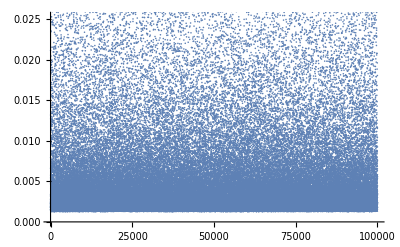

```mathematica
ListPlot[Table[{i,Purity[[i]]},{i,10^5}]]
```

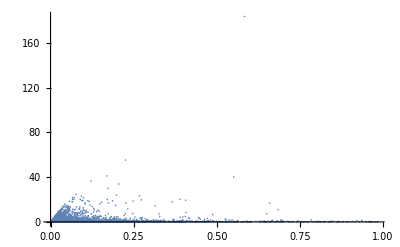

```mathematica
ListPlot[Table[{Purity[[i]],Max[0,Negativity[[i]]]},{i,10^5}],PlotRange->All]
(*Yesterday max value on y axis was about 40, now is nearly 200*)
```

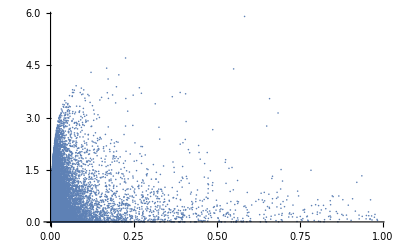

```mathematica
ListPlot[Table[{Purity[[i]],Max[0,LogNeg[[i]]]},{i,10^5}],PlotRange->All]
(*Yesterday max value on y axis was about 4, now is around 6*)
```